#### Code

```mathematica
(* Brute force construction of all Graphs on n vertices up to Isomorphism*)
allEdges[n_]:=Flatten[Table[UndirectedEdge[i,j],{i,1,n},{j,i+1,n}]];
allConnected[n_]:=Select[Map[Graph[Range[n],#,VertexLabels->Automatic]&,Subsets[allEdges[n]]],ConnectedGraphQ];
allConnectedUpToIso[n_]:=DeleteDuplicates[allConnected[n],IsomorphicGraphQ];
(*Helper Functions*)
PerfectDistanceQ[G_]:=Union[Flatten[Round[GraphDistanceMatrix[G]]]] == Range[0,Binomial[VertexCount[G],2]]
WeightsList[G_]:=Flatten[Permutations[#]&/@Select[Subsets[Range[Binomial[VertexCount[G],2]],{EdgeCount[G]}],MemberQ[#,1]&&MemberQ[#,2]&],1]
```

```mathematica
(*Construct Graph Sets*)
vertex6=allConnectedUpToIso[6];
(*vertex6=allConnectedUpToIso[6];*)
```

```mathematica
(*
 vertex5 should take around a second
vertex6 took around 8 minutes on my laptop
*)
(*CHOOSE SET OF GRAPHS TO TEST*)
GraphList = vertex6;

MinimalPerfectDistanceGraphs = {};
NotPerfectDistanceGraphs = {};

AbsoluteTiming[
While[Length[GraphList]>0,
G = First[GraphList];
GraphList = Delete[GraphList,1];

(* Test weights until a PDG is found or weights exausted*)
(*PerfectDistanceGraph = Null if G does not support a perfect distance weighting*)
WL = WeightsList[G];

PerfectDistanceGraph = Catch[Do[If[PerfectDistanceQ[Graph[EdgeList[G],EdgeWeight->WL[[j]]]],Throw[G]],{j,1,Length[WL]}]];

(*Update MPDG and NPD: Comparisions to Null are probelmatic*)
If[Head[PerfectDistanceGraph]==Graph, AppendTo[MinimalPerfectDistanceGraphs,PerfectDistanceGraph]];
If[PerfectDistanceGraph==Null,AppendTo[NotPerfectDistanceGraphs,G]];

(*Trim Graph List*)
GraphList = Select[GraphList,Not[IsomorphicSubgraphQ[PerfectDistanceGraph,#]]&];
];
]

Print["Minimal Perfect Distance Graphs: "]
TableForm[MinimalPerfectDistanceGraphs,TableDirections->Row]

Print["Not Perfect Distance Graphs: "]
TableForm[NotPerfectDistanceGraphs,TableDirections->Row]
```

{387.503,Null}

Minimal Perfect Distance Graphs:

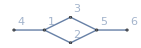
```mathematica
{{-Graphics-, -Graphics-, -Graphics-, -Graphics-}}
```

\n(*GridBox[{{GraphicsBox[NamespaceBox["NetworkGraphics",DynamicModuleBox[{Typeset`graph = HoldComplete[
Graph[{1, 2, 3, 4, 5, 6}, {Null, {{1, 2}, {1, 3}, {1, 4}, {2, 5}, {3, 6}, {5, 6}}}, {VertexLabels -> {Automatic}}]]}, TagBox[GraphicsGroupBox[{{Hue[0.6, 0.7, 0.5], Opacity[0.7], Arrowheads[0.], ArrowBox[{{{1.0272268301699605`, 0.6720167569740376}, {1.8310644578447695`, 0.}}, {{1.0272268301699605`, 0.6720167569740376}, {1.8312318901342532`, 1.3440431854486032`}}, {{1.0272268301699605`, 0.6720167569740376}, {0., 0.6722959332846047}}, {{1.8310644578447695`, 0.}, {2.7840622385070075`, 0.21343390529103207`}}, {{1.8312318901342532`, 1.3440431854486032`}, {2.7841602102994347`, 1.1308961692173485`}}, {{2.7840622385070075`, 0.21343390529103207`}, {2.7841602102994347`, 1.1308961692173485`}}}, 0.028671404882950363`]}, {Hue[0.6, 0.2, 0.8], EdgeForm[{GrayLevel[0], Opacity[0.7]}], {DiskBox[{1.0272268301699605`, 0.6720167569740376}, 0.028671404882950363], InsetBox["1", Offset[{2, 2}, {1.055898235052911, 0.700688161856988}], ImageScaled[{0, 0}],BaseStyle->"Graphics"]}, {DiskBox[{1.8310644578447695`, 0.}, 0.028671404882950363], InsetBox["2", Offset[{2, 2}, {1.8597358627277198, 0.028671404882950363}], ImageScaled[{0, 0}],BaseStyle->"Graphics"]}, {DiskBox[{1.8312318901342532`, 1.3440431854486032`}, 0.028671404882950363], InsetBox["3", Offset[{2, 2}, {1.8599032950172036, 1.3727145903315536}], ImageScaled[{0, 0}],BaseStyle->"Graphics"]}, {DiskBox[{0., 0.6722959332846047}, 0.028671404882950363], InsetBox["4", Offset[{2, 2}, {0.028671404882950363, 0.7009673381675551}], ImageScaled[{0, 0}],BaseStyle->"Graphics"]}, {DiskBox[{2.7840622385070075`, 0.21343390529103207`}, 0.028671404882950363], InsetBox["5", Offset[{2, 2}, {2.812733643389958, 0.24210531017398243}], ImageScaled[{0, 0}],BaseStyle->"Graphics"]}, {DiskBox[{2.7841602102994347`, 1.1308961692173485`}, 0.028671404882950363], InsetBox["6", Offset[{2, 2}, {2.812831615182385, 1.1595675741002989}], ImageScaled[{0, 0}],BaseStyle->"Graphics"]}}}],MouseAppearanceTag["NetworkGraphics"]],AllowKernelInitialization->False]],DefaultBaseStyle->"NetworkGraphics",FormatType->TraditionalForm,FrameTicks->None,ImageSize->{120.03021240234375`, Automatic}], GraphicsBox[NamespaceBox["NetworkGraphics",DynamicModuleBox[{Typeset`graph = HoldComplete[
Graph[{1, 2, 3, 4, 5, 6}, {Null, {{1, 2}, {1, 3}, {2, 4}, {3, 5}, {4, 6}, {5, 6}}}, {VertexLabels -> {Automatic}}]]}, TagBox[GraphicsGroupBox[{{Hue[0.6, 0.7, 0.5], Opacity[0.7], Arrowheads[0.], ArrowBox[{{{-0.8660254037844389, 0.5000000000000008}, {1.8369701987210297`*^-16, 1.}}, {{-0.8660254037844389, 0.5000000000000008}, {-0.8660254037844384, -0.4999999999999994}}, {{1.8369701987210297`*^-16, 1.}, {0.8660254037844386, 0.4999999999999993}}, {{-0.8660254037844384, -0.4999999999999994}, {3.8285686989269494`*^-16, -1.}}, {{0.8660254037844386, 0.4999999999999993}, {0.8660254037844389, -0.5000000000000012}}, {{3.8285686989269494`*^-16, -1.}, {0.8660254037844389, -0.5000000000000012}}}, 0.02261146496815286]}, {Hue[0.6, 0.2, 0.8], EdgeForm[{GrayLevel[0], Opacity[0.7]}], {DiskBox[{-0.8660254037844389, 0.5000000000000008}, 0.02261146496815286], InsetBox["1", Offset[{2, 2}, {-0.843413938816286, 0.5226114649681537}], ImageScaled[{0, 0}],BaseStyle->"Graphics"]}, {DiskBox[{1.8369701987210297`*^-16, 1.}, 0.02261146496815286], InsetBox["2", Offset[{2, 2}, {0.022611464968153045, 1.0226114649681528}], ImageScaled[{0, 0}],BaseStyle->"Graphics"]}, {DiskBox[{-0.8660254037844384, -0.4999999999999994}, 0.02261146496815286], InsetBox["3", Offset[{2, 2}, {-0.8434139388162856, -0.47738853503184653}], ImageScaled[{0, 0}],BaseStyle->"Graphics"]}, {DiskBox[{0.8660254037844386, 0.4999999999999993}, 0.02261146496815286], InsetBox["4", Offset[{2, 2}, {0.8886368687525914, 0.5226114649681521}], ImageScaled[{0, 0}],BaseStyle->"Graphics"]}, {DiskBox[{3.8285686989269494`*^-16, -1.}, 0.02261146496815286], InsetBox["5", Offset[{2, 2}, {0.022611464968153243, -0.9773885350318472}], ImageScaled[{0, 0}],BaseStyle->"Graphics"]}, {DiskBox[{0.8660254037844389, -0.5000000000000012}, 0.02261146496815286], InsetBox["6", Offset[{2, 2}, {0.8886368687525918, -0.47738853503184836}], ImageScaled[{0, 0}],BaseStyle->"Graphics"]}}}],MouseAppearanceTag["NetworkGraphics"]],AllowKernelInitialization->False]],DefaultBaseStyle->"NetworkGraphics",FormatType->TraditionalForm,FrameTicks->None,ImageSize->{73.8701171875, Automatic}]}
},GridBoxAlignment->{"Columns" -> {{Left}}, "Rows" -> {{Baseline}}},GridBoxSpacings->{"Columns" -> {
Offset[0.27999999999999997`], {
Offset[0.7]}, 
Offset[0.27999999999999997`]}, "Rows" -> {
Offset[0.2], {
Offset[0.4]}, 
Offset[0.2]}}])\n\nNot Perfect Distance Graphs:

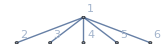
```mathematica
{{-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-}}
```